```mathematica
<<VasilDimitrov`SolutionsX`
```

## Setup

```mathematica
sol=Retrieve["CCLP_5dL_Hopf-cη_Original_vasko-Mac-15232"];
Load@sol
```

Loaded | sol | man | gg | ee | ηη | ωω | curved | flat | spin | fA | AA | fF | FF | ϵϵ | Δr | Δη | ρ2 | f | a | b | m | q | g | α | Ξa | Ξb | ϵ01 | ϵ02 | ϵ03 | ϵ04 | Cx | "coord" | "const" | 𝔼gg | 𝔼AA

```mathematica
sol[$info,"CCLP",Version]="Thermodynamics"
```

Thermodynamics

```mathematica
Store@sol
```

## Calculate thermodynamic quantities

### Energy (and horizons)

```mathematica
IncludeTo[sol[$constant],<|Symbol->rp|>]
IncludeTo[sol[$assumption],<|Symbol->"thermo",Value->{rp>0}|>]
```

Loaded | sol[$constant] | rp

Unloaded | sol[$assumption] | "thermo"

Loaded | sol[$assumption] | "thermo"

```mathematica
sol[$chart,curved,Coord]
```

{t,r,cη,ξ1,ξ2}

```mathematica
sol[$assumption,"coord"]
```

<|Symbol→coord,Value→{t∈ℝ,0<r,0<cη<1,0≤ξ1<2 π,0≤ξ2<2 π}|>

```mathematica
First@Solve[(Δr[rp]/.sol[$rule,"func",Value])==0,m,Assumptions->True]
IncludeTo[sol[$rule],<|Symbol->"mTrp",Value->%|>]
```

{m→(2 a b q+q^2+(a^2+rp^2) (b^2+rp^2) (1+g^2 rp^2))/(2 rp^2)}

```mathematica
Sval=(π^2((rp^2+a^2)(rp^2+b^2)+a b q))/(2Ξa Ξb rp G5)/.sol[$rule,"const",Value]
```

(π^2 (a b q+(a^2+rp^2) (b^2+rp^2)))/(2 (1-a^2 g^2) (1-b^2 g^2) G5 rp)

{g→434,m→89,a→-11/9741,b→2536/1128101,q→53/2}

{-0.341025+0.194308 ⅈ,0.341025-0.194308 ⅈ,-0.341025-0.194308 ⅈ,0.341025+0.194308 ⅈ,0.-0.396354 ⅈ,0.+0.396354 ⅈ}

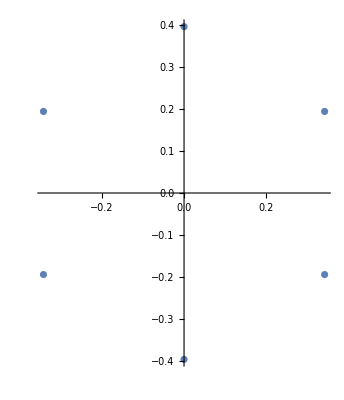

```mathematica
Last@FindInstance[Drop[sol[$assumption,"const",Value],{3}],{g,m,a,b,q},Reals,5,RandomSeeding->Automatic]
Solve[m==(m/.sol[$rule,"mTrp",Value]),rp,Assumptions->True]//Simplify//Values//Flatten;
%/.%%//Simplify//N//Chop
ComplexListPlot[%]
```

```mathematica
sol[$metric,gg,Expr]/.Diff[t[]]->0/.Diff[r[]]->0/.sol[$rule,"func",Value]/.sol[$rule,"const",Value]/.sol[$rule,"mTrp",Value]/.r[]->rp
MakeArray[sol,%,Drop[sol[$chart,curved,Coord],{1,2}]]//Simplify;
Simplify@√(Simplify@Det@%)/.Abs[x_]:>x
Integrate[1/(4G5)%,{cη[],0,1},{ξ1[],0,2π},{ξ2[],0,2π}]
%-Sval//Simplify
```

((b^2+rp^2) d[ξ2]⊗d[ξ2] cη^2)/(1-b^2 g^2)+((a^2+rp^2) d[ξ1]⊗d[ξ1] (1-cη^2))/(1-a^2 g^2)+(d[cη]⊗d[cη] (rp^2+a^2 cη^2+b^2 (1-cη^2)))/((1-cη^2) (1-a^2 g^2 cη^2-b^2 g^2 (1-cη^2)))+(2 q ((a b d[ξ2]⊗d[ξ2] cη^4)/(1-b^2 g^2)+(b^2 d[ξ1]⊗d[ξ2] cη^2 (1-cη^2))/(1-b^2 g^2)+(a^2 d[ξ2]⊗d[ξ1] cη^2 (1-cη^2))/(1-a^2 g^2)+(a b d[ξ1]⊗d[ξ1] (1-cη^2)^2)/(1-a^2 g^2)))/(rp^2+a^2 cη^2+b^2 (1-cη^2))+(((b^2 d[ξ2]⊗d[ξ2] cη^4)/((1-b^2 g^2)^2)+(a b d[ξ1]⊗d[ξ2] cη^2 (1-cη^2))/((1-a^2 g^2) (1-b^2 g^2))+(a b d[ξ2]⊗d[ξ1] cη^2 (1-cη^2))/((1-a^2 g^2) (1-b^2 g^2))+(a^2 d[ξ1]⊗d[ξ1] (1-cη^2)^2)/((1-a^2 g^2)^2)) (-q^2+(2 a b g^2 q+(2 a b q+q^2+(a^2+rp^2) (b^2+rp^2) (1+g^2 rp^2))/rp^2) (rp^2+a^2 cη^2+b^2 (1-cη^2))))/((rp^2+a^2 cη^2+b^2 (1-cη^2))^2)

((a b q+a^2 (b^2+rp^2)+rp^2 (b^2+rp^2)) cη)/((-1+a^2 g^2) (-1+b^2 g^2) rp)

(π^2 (a b q+a^2 (b^2+rp^2)+rp^2 (b^2+rp^2)))/(2 (-1+a^2 g^2) (-1+b^2 g^2) G5 rp)

0

### Angular momenta

```mathematica
J1val=(π(2a m+b q(1+a^2 g^2)))/(4 Ξa^2 Ξb G5)/.sol[$rule,"const",Value]
J2val=(π(2b m+a q(1+b^2 g^2)))/(4Ξa Ξb^2 G5)/.sol[$rule,"const",Value]
```

(π (2 a m+b (1+a^2 g^2) q))/(4 (1-a^2 g^2)^2 (1-b^2 g^2) G5)

(π (2 b m+a (1+b^2 g^2) q))/(4 (1-a^2 g^2) (1-b^2 g^2)^2 G5)

```mathematica
ToBasis[curved]@ToBasis[curved]@(epsilongg[{2,-curved},{3,-curved},{4,-curved},-𝒶,-𝒷]gg[𝒶,𝓍]gg[𝒷,𝓎]PD[-𝓍][gg[-𝓎,{3,-curved}]])/.epsilonToetaDown[gg,curved]
ToArray[sol]@%//Simplify;
Normal@Series[%,{r[],∞,0}]
1/(16π G5)Integrate[%,{cη[],0,1},{ξ1[],0,2π},{ξ2[],0,2π}]
%-J1val//Simplify
```

√(-g^OverTilde[~]) η_~ |   |   |   |   |  
2 | 3 | 4 | 𝒶 | 𝒷 g | 𝒶 | 𝒸
  |   g | 𝒷 | 𝒹
  |   ∂_𝒸 g |   |  
𝒹 | 3

(4 (2 a m+b q+a^2 b g^2 q) cη (-1+cη^2))/((-1+a^2 g^2)^2 (-1+b^2 g^2))

-(π (2 a m+b q+a^2 b g^2 q))/(4 (-1+a^2 g^2)^2 (-1+b^2 g^2) G5)

0

```mathematica
ToBasis[curved]@ToBasis[curved]@(epsilongg[{2,-curved},{3,-curved},{4,-curved},-𝒶,-𝒷]gg[𝒶,𝓍]gg[𝒷,𝓎]PD[-𝓍][gg[-𝓎,{4,-curved}]])/.epsilonToetaDown[gg,curved]
ToArray[sol]@%//Simplify;
Normal@Series[%,{r[],∞,0}]
1/(16π G5)Integrate[%,{cη[],0,1},{ξ1[],0,2π},{ξ2[],0,2π}]
%-J2val//Simplify
```

√(-g^OverTilde[~]) η_~ |   |   |   |   |  
2 | 3 | 4 | 𝒶 | 𝒷 g | 𝒶 | 𝒸
  |   g | 𝒷 | 𝒹
  |   ∂_𝒸 g |   |  
𝒹 | 4

-(4 (2 b m+a q+a b^2 g^2 q) cη^3)/((-1+a^2 g^2) (-1+b^2 g^2)^2)

-(π (2 b m+a q+a b^2 g^2 q))/(4 (-1+a^2 g^2) (-1+b^2 g^2)^2 G5)

0

### Electric charge

```mathematica
fF[]⋀fA[]
%/.(sol[$form,#,Symbol]->sol[$form,#,Expr]&/@Keys@sol[$form])/.sol[$rule,"func",Value]/.sol[$rule,"const",Value]//Simplification;
Coefficient[%,Diff[cη[]]⋀Diff[ξ1[]]⋀Diff[ξ2[]]]
Series[%,{r[],∞,0}]
```

fF⋀fA

-(6 a b q^2 cη)/(Cx^2 (-1+a^2 g^2) (-1+b^2 g^2) (a^2 cη^2-b^2 (-1+cη^2)+r^2)^2)

O[1/r]^4

```mathematica
Qval=(Cx √3 π q)/(4Ξa Ξb G5)/.sol[$rule,"const",Value]
```

(√3 Cx π q)/(4 (1-a^2 g^2) (1-b^2 g^2) G5)

```mathematica
ToBasis[curved]@ToBasis[curved]@(1/(2!)epsilongg[{2,-curved},{3,-curved},{4,-curved},-𝒶,-𝒷]FF[𝒶,𝒷])/.epsilonToetaDown[gg,curved]
Simplify@ToArray[sol]@%;
Normal@Series[%,{r[],∞,0}]
-Cx^2/(16π G5)Integrate[%,{cη[],0,1},{ξ1[],0,2π},{ξ2[],0,2π}]
%-Qval//Simplify
```

1/2 √(-g^OverTilde[~]) η_~ |   |   |   |   |  
2 | 3 | 4 | 𝒶 | 𝒷 FF | 𝒶 | 𝒷
  |

-(2 √3 q cη)/(Cx (-1+a^2 g^2) (-1+b^2 g^2))

(√3 Cx π q)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5)

0

### Potentials from the Killing vector

```mathematica
Ω1val=(a(rp^2+b^2)(1+g^2 rp^2)+b q)/((rp^2+a^2)(rp^2+b^2)+a b q)
Ω2val=Ω1val/.{a->b,b->a}
βval=(2π rp((rp^2+a^2)(rp^2+b^2)+a b q))/(rp^4(1+g^2(2 rp^2+a^2+b^2))-(a b+q)^2)
```

(b q+a (b^2+rp^2) (1+g^2 rp^2))/(a b q+(a^2+rp^2) (b^2+rp^2))

(a q+b (a^2+rp^2) (1+g^2 rp^2))/(a b q+(a^2+rp^2) (b^2+rp^2))

(2 π rp (a b q+(a^2+rp^2) (b^2+rp^2)))/(-(a b+q)^2+rp^4 (1+g^2 (a^2+b^2+2 rp^2)))

```mathematica
IncludeTo[sol[$constant],{<|Symbol->β|>,<|Symbol->Ω1|>,<|Symbol->Ω2|>}]
IncludeTo[sol[$assumption],<|Symbol->"thermo",Value->{rp>0,β>0}|>]
IncludeTo[sol[$tensor],<|Symbol->VV[𝒶]|>]
```

Loaded | sol[$constant] | β | Ω1 | Ω2

Unloaded | sol[$assumption] | "thermo"

Loaded | sol[$assumption] | "thermo"

Loaded | sol[$tensor] | VV

```mathematica
sol[$tensor,VV,Routine]=<|
Seed->Hold[ToArray[$solution][$array]],
Chain->{
Seed->{{1}},
{{1}}->{{-1}}
},
Map->$Map,
ParallelMap->$ParallelMap
|>
```

<|Seed→Hold[ToArray[$solution][$array]],Chain→{Seed→{{1}},{{1}}→{{-1}}},Map→Together,ParallelMap→Simplify|>

```mathematica
$Map=Together[#/.sol[$rule,"func",Value]/.sol[$rule,"const",Value]]&
```

Together[#1/.sol[$rule,func,Value]/.sol[$rule,const,Value]]&

```mathematica
$array={1,0,0,Ω1,Ω2};
Compute@sol[$tensor,VV]
```

Applied Together and Simplify to VV | 𝒶
 ==Hold[ToArray[$solution][$array]] in 0 10

Applied Together and Simplify to   VV |  
𝒶 in 0 5

```mathematica
ToArray[sol]@CovDToChristoffel@(cd[-𝒶][VV[-𝒷]]+cd[-𝒷][VV[-𝒶]])//Simplify
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
ToArray[sol]@(VV[-𝒶]VV[𝒶])/.sol[$rule,"mTrp",Value];
Normal@Simplify@Series[%,{r[],rp,0},{cη[],0,0}]
First@Solve[%==0,Ω1,Assumptions->True]
Ω1-Ω1val/.%//Simplify
```

((-b q+b^2 rp^2 Ω1+rp^4 Ω1+a^2 (b^2+rp^2) Ω1-a (rp^2+g^2 rp^4+b^2 (1+g^2 rp^2)-b q Ω1))^2)/((-1+a^2 g^2)^2 rp^2 (b^2+rp^2)^2)

{Ω1→(a b^2+b q+a rp^2+a b^2 g^2 rp^2+a g^2 rp^4)/(a^2 b^2+a b q+a^2 rp^2+b^2 rp^2+rp^4)}

0

```mathematica
ToArray[sol]@(VV[-𝒶]VV[𝒶])/.sol[$rule,"mTrp",Value]/.Ω1->Ω1val;
Normal@Simplify@Series[%,{r[],rp,0},{cη[],0,2}]
First@Solve[%==0,Ω2,Assumptions->True]
Ω2-Ω2val/.%//Simplify
```

-((b^2+rp^2) (a q (-1+b Ω2)+a^2 (-b (1+g^2 rp^2)+b^2 Ω2+rp^2 Ω2)+rp^2 (-b (1+g^2 rp^2)+b^2 Ω2+rp^2 Ω2))^2 cη^2)/((-1+b^2 g^2) (a b q+a^2 (b^2+rp^2)+rp^2 (b^2+rp^2))^2)

{Ω2→(a^2 b+a q+b rp^2+a^2 b g^2 rp^2+b g^2 rp^4)/(a^2 b^2+a b q+a^2 rp^2+b^2 rp^2+rp^4)}

0

```mathematica
ToArray[sol]@(VV[-𝒶]VV[𝒶])/.sol[$rule,"mTrp",Value]/.Ω1->Ω1val/.Ω2->Ω2val;
Normal@Simplify@Series[%,{r[],rp,0}]
```

0

```mathematica
Φval=(√3 q rp^2)/(Cx((rp^2+a^2)(rp^2+b^2)+a b q))
```

(√3 q rp^2)/(Cx (a b q+(a^2+rp^2) (b^2+rp^2)))

```mathematica
ToArray[sol]@(VV[𝒶]AA[-𝒶])/.Ω1->Ω1val/.Ω2->Ω2val;
Collect[Normal@Simplify@Series[%,{r[],rp,0}],α,Simplify]
Normal@Simplify@Series[%%,{r[],∞,0}]
%%-%
%-Φval//Simplify
```

(√3 q rp^2)/(Cx (a b q+a^2 (b^2+rp^2)+rp^2 (b^2+rp^2)))+α

α

(√3 q rp^2)/(Cx (a b q+a^2 (b^2+rp^2)+rp^2 (b^2+rp^2)))

0

```mathematica
ToArray[sol]@(AA[𝒶]AA[-𝒶])/.sol[$rule,"mTrp",Value];
Normal@Simplify@Series[%,{r[],rp,-1}]
solα=First@Solve[%==0,α,Assumptions->True]
α+Φval/.%//Simplify
```

-(Cx^2 (a^2+rp^2)^2 (b^2+rp^2)^2 α^2+2 Cx q (a^2+rp^2) (b^2+rp^2) α (√3 rp^2+a b Cx α)+q^2 (3 rp^4+2 √3 a b Cx rp^2 α+a^2 b^2 Cx^2 α^2))/(2 Cx^2 rp (-2 a b q-q^2+rp^4 (1+b^2 g^2+2 g^2 rp^2)+a^2 (-b^2+g^2 rp^4)) (rp^2+a^2 cη^2-b^2 (-1+cη^2)) (-rp+r))

{α→-(√3 q rp^2)/(Cx (a^2 b^2+a b q+a^2 rp^2+b^2 rp^2+rp^4))}

0

```mathematica
IncludeTo[sol[$rule],<|Symbol->"α",Value->solα|>]
```

### Energy from the 1st law

```mathematica
Eval=(m π(2Ξa+2Ξb-Ξa Ξb)+2π q a b g^2(Ξa+Ξb))/(4G5 Ξa^2 Ξb^2)/.sol[$rule,"const",Value]
```

((2 (1-a^2 g^2)+2 (1-b^2 g^2)-(1-a^2 g^2) (1-b^2 g^2)) m π+2 a b g^2 (2-a^2 g^2-b^2 g^2) π q)/(4 (1-a^2 g^2)^2 (1-b^2 g^2)^2 G5)

```mathematica
1/β Hold[D[S,#]]+Ω1 Hold[D[J1,#]]+Ω2 Hold[D[J2,#]]+Φ Hold[D[Q,#]]-Hold[D[EE,#]]&/@{a,b,q,rp}
%/.{EE->Eval,S->Sval,J1->J1val,J2->J2val,Q->Qval,β->βval,Ω1->Ω1val,Ω2->Ω2val,Φ->Φval}/.sol[$rule,"mTrp",Value]//ReleaseHold//FullSimplify
```

{-Hold[∂_a EE]+Ω1 Hold[∂_a J1]+Ω2 Hold[∂_a J2]+Φ Hold[∂_a Q]+Hold[∂_a S]/β,-Hold[∂_b EE]+Ω1 Hold[∂_b J1]+Ω2 Hold[∂_b J2]+Φ Hold[∂_b Q]+Hold[∂_b S]/β,-Hold[∂_q EE]+Ω1 Hold[∂_q J1]+Ω2 Hold[∂_q J2]+Φ Hold[∂_q Q]+Hold[∂_q S]/β,-Hold[∂_rp EE]+Ω1 Hold[∂_rp J1]+Ω2 Hold[∂_rp J2]+Φ Hold[∂_rp Q]+Hold[∂_rp S]/β}

{0,0,0,0}

### On-shell action

```mathematica
sol[$metric,gg,Expr]/.sol[$rule,"func",Value]/.sol[$rule,"const",Value];
%/.m->0/.q->0
%%/.m->0/.q->0/.a->0/.b->0/.{r[]->√(((1-cη[]^2)(a^2+r[]^2))/(1-a^2 g^2)+(cη[]^2(b^2+r[]^2))/(1-b^2 g^2)),cη[]->√(1-1/(1-((-1+a^2 g^2) cη^2 (b^2+r^2))/((-1+b^2 g^2) (-1+cη^2) (a^2+r^2))))};
%%-%//Simplification
```

(d[ξ1]⊗d[ξ1] (1-cη^2) (a^2+r^2))/(1-a^2 g^2)+(d[ξ2]⊗d[ξ2] cη^2 (b^2+r^2))/(1-b^2 g^2)+(d[cη]⊗d[cη] (a^2 cη^2+b^2 (1-cη^2)+r^2))/((1-cη^2) (1-a^2 g^2 cη^2-b^2 g^2 (1-cη^2)))+(d[r]⊗d[r] r^2 (a^2 cη^2+b^2 (1-cη^2)+r^2))/((a^2+r^2) (b^2+r^2) (1+g^2 r^2))-(d[t]⊗d[t] (1-a^2 g^2 cη^2-b^2 g^2 (1-cη^2)) (1+g^2 r^2))/((1-a^2 g^2) (1-b^2 g^2))

0

```mathematica
Keys@sol[$constant]
```

{a,b,m,q,g,α,Ξa,Ξb,ϵ01,ϵ02,ϵ03,ϵ04,Cx,rp,β,Ω1,Ω2}

```mathematica
sol[$assumption]
```

<|coord→<|Symbol→coord,Value→{t∈ℝ,0<r,0<cη<1,0≤ξ1<2 π,0≤ξ2<2 π}|>,const→<|Symbol→const,Value→{0<g,0<m,α∈ℝ,-1<a g<1,-1<b g<1,0<a+b+a b g,0<q<m/(1+a g+b g)}|>,thermo→<|Symbol→thermo,Value→{rp>0,β>0}|>|>

```mathematica
IncludeTo[sol[$constant],{<|Symbol->R0|>,<|Symbol->G5|>}]
IncludeTo[sol[$assumption],<|Symbol->"thermo",Value->{rp>0,β>0,R0>0,G5>0}|>]
```

Loaded | sol[$constant] | R0 | G5

Unloaded | sol[$assumption] | "thermo"

Loaded | sol[$assumption] | "thermo"

```mathematica
MakeArray[sol,sol[$metric,gg,Expr]/.sol[$rule,"func",Value]/.sol[$rule,"const",Value]/.r[]->R0/.q->0/.m->0,{t[],cη[],ξ1[],ξ2[]}]//MatrixForm
```

(-((1+g^2 R0^2) (1-a^2 g^2 cη^2-b^2 g^2 (1-cη^2)))/((1-a^2 g^2) (1-b^2 g^2)) | 0 | 0 | 0
0 | (R0^2+a^2 cη^2+b^2 (1-cη^2))/((1-cη^2) (1-a^2 g^2 cη^2-b^2 g^2 (1-cη^2))) | 0 | 0
0 | 0 | ((a^2+R0^2) (1-cη^2))/(1-a^2 g^2) | 0
0 | 0 | 0 | ((b^2+R0^2) cη^2)/(1-b^2 g^2))

```mathematica
MakeArray[sol,sol[$metric,gg,Expr]/.sol[$rule,"func",Value]/.sol[$rule,"const",Value]/.r[]->R0,{t[],cη[],ξ1[],ξ2[]}];
√(-Det@%)//Simplify
Normal@Series[%,{R0,∞,0}];
β Integrate[%,{cη[],0,1},{ξ1[],0,2π},{ξ2[],0,2π}];
volbh=Normal@Series[%,{R0,∞,0}]
```

√(((2 a b q+q^2+a^2 (b^2+R0^2) (1+g^2 R0^2)+R0^2 (b^2-2 m+R0^2+b^2 g^2 R0^2+g^2 R0^4)) cη^2 (R0^2+a^2 cη^2-b^2 (-1+cη^2)))/((-1+a^2 g^2)^2 (-1+b^2 g^2)^2))

((-3-g^2 (-9 a^2-9 b^2+a^4 g^2-11 a^2 b^2 g^2+b^4 g^2+24 m)) π^2 β)/(12 g^3 (-1+a^2 g^2) (-1+b^2 g^2))+((2+3 (a^2+b^2) g^2) π^2 R0^2 β)/(2 g (-1+a^2 g^2) (-1+b^2 g^2))+(2 g π^2 R0^4 β)/((-1+a^2 g^2) (-1+b^2 g^2))

```mathematica
MakeArray[sol,sol[$metric,gg,Expr]/.sol[$rule,"func",Value]/.sol[$rule,"const",Value]/.r[]->R0/.q->0/.m->0,{t[],cη[],ξ1[],ξ2[]}];
√(-Det@%)//Simplify
Normal@Series[%,{R0,∞,0}];
τupper Integrate[%,{cη[],0,1},{ξ1[],0,2π},{ξ2[],0,2π}];
volads=Normal@Series[%,{R0,∞,0}]
```

√(((a^2+R0^2) (b^2+R0^2) (1+g^2 R0^2) cη^2 (R0^2+a^2 cη^2-b^2 (-1+cη^2)))/((-1+a^2 g^2)^2 (-1+b^2 g^2)^2))

((-3-g^2 (-9 a^2-9 b^2+a^4 g^2-11 a^2 b^2 g^2+b^4 g^2)) π^2 τupper)/(12 g^3 (-1+a^2 g^2) (-1+b^2 g^2))+((2+3 (a^2+b^2) g^2) π^2 R0^2 τupper)/(2 g (-1+a^2 g^2) (-1+b^2 g^2))+(2 g π^2 R0^4 τupper)/((-1+a^2 g^2) (-1+b^2 g^2))

```mathematica
volbh-volads//Simplify
Flatten@Solve[%==0,τupper,Assumptions->True];
τupperRule=Normal@(Normal@Simplify@Series[#,{R0,∞,4}]&/@Association@%)
```

1/(12 g^3 (-1+a^2 g^2) (-1+b^2 g^2))π^2 ((-3-a^4 g^4-b^4 g^4+24 g^4 R0^4+3 g^2 (-8 m+4 R0^2)+a^2 g^2 (9+11 b^2 g^2+18 g^2 R0^2)+9 b^2 (g^2+2 g^4 R0^2)) β+(a^4 g^4+b^4 g^4-a^2 g^2 (9+11 b^2 g^2+18 g^2 R0^2)-9 b^2 (g^2+2 g^4 R0^2)-3 (-1+4 g^2 R0^2+8 g^4 R0^4)) τupper)

{τupper→β-(m β)/(g^2 R0^4)}

```mathematica
First@Solve[(√(((1-cη[]^2)(a^2+r[]^2))/(1-a^2 g^2)+(cη[]^2(b^2+r[]^2))/(1-b^2 g^2))/.r[]^2:>r2)==0,r2,Assumptions->True]
rlowerRule={rlower->√(First@Values@%)}
```

{r2→(a^2-a^2 b^2 g^2-a^2 cη^2+b^2 cη^2)/(-1+b^2 g^2+a^2 g^2 cη^2-b^2 g^2 cη^2)}

{rlower→√((a^2-a^2 b^2 g^2-a^2 cη^2+b^2 cη^2)/(-1+b^2 g^2+a^2 g^2 cη^2-b^2 g^2 cη^2))}

```mathematica
√(-Detggcurved[])(RicciScalarcd[]+12 g^2-Cx^2/4 FF[𝒶,𝒷]FF[-𝒶,-𝒷])+Cx^3/(12 √3)etaUpcurved[𝓂,𝒶,𝒷,𝒸,𝒹]AA[-𝓂]FF[-𝒶,-𝒷]FF[-𝒸,-𝒹]
Simplify@ToArray[sol]@%;
Integrate[%,r[]];
Normal@Simplify@Series[(%/.r[]->R0)-(%/.r[]->rp),{R0,∞,0}];
Integrate[%,cη[]];
(%/.cη[]->1)-(%/.cη[]->0);
-1/(16π G5)β Integrate[%,{ξ1[],0,2π},{ξ2[],0,2π}];
resbh=Normal@Simplify@Series[%,{R0,∞,0}]
```

(Cx^3 AA |  
𝓂 η̃ | 𝓂 | 𝒶 | 𝒷 | 𝒸 | 𝒹
  |   |   |   |   FF |   |  
𝒶 | 𝒷 FF |   |  
𝒸 | 𝒹)/(12 √3)+√(-g^OverTilde[~]) (12 g^2-1/4 Cx^2 FF |   |  
𝒶 | 𝒷 FF | 𝒶 | 𝒷
  |  +R[▽])

((a^2+b^2) g^2 π R0^2 β)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5)+(g^2 π R0^4 β)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5)-(π (3 a^4 g^2 rp^2 (b^2+rp^2)+3 a^2 g^2 rp^2 (b^4+3 b^2 rp^2+2 rp^4)+3 rp^2 (q^2+g^2 rp^2 (b^2+rp^2)^2)+√3 a b Cx q^2 α) β)/(12 (-1+a^2 g^2) (-1+b^2 g^2) G5 (a^2+rp^2) (b^2+rp^2))

```mathematica
√(-Detggcurved[])(RicciScalarcd[]+12 g^2-Cx^2/4 FF[𝒶,𝒷]FF[-𝒶,-𝒷])+Cx^3/(12 √3)etaUpcurved[𝓂,𝒶,𝒷,𝒸,𝒹]AA[-𝓂]FF[-𝒶,-𝒷]FF[-𝒸,-𝒹]
Simplify@ToArray[sol]@%/.m->0/.q->0;
Integrate[%,r[]];
Normal@Simplify@Series[(%/.r[]->R0)-(%/.r[]->rlower/.rlowerRule),{R0,∞,0}];
Integrate[%,cη[]];
(%/.cη[]->1)-(%/.cη[]->0);
-1/(16π G5)τupper Integrate[%,{ξ1[],0,2π},{ξ2[],0,2π}]/.τupperRule;
resads=Normal@Simplify@Series[%,{R0,∞,0}]
```

(Cx^3 AA |  
𝓂 η̃ | 𝓂 | 𝒶 | 𝒷 | 𝒸 | 𝒹
  |   |   |   |   FF |   |  
𝒶 | 𝒷 FF |   |  
𝒸 | 𝒹)/(12 √3)+√(-g^OverTilde[~]) (12 g^2-1/4 Cx^2 FF |   |  
𝒶 | 𝒷 FF | 𝒶 | 𝒷
  |  +R[▽])

((a^2 b^2 g^2-m) π β)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5)+((a^2+b^2) g^2 π R0^2 β)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5)+(g^2 π R0^4 β)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5)

```mathematica
Ival=(π β)/(4Ξa Ξb G5)(m-g^2(rp^2+a^2)(rp^2+b^2)-(q^2 rp^2)/((rp^2+a^2)(rp^2+b^2)+a b q))/.sol[$rule,"const",Value]
```

(π (m-g^2 (a^2+rp^2) (b^2+rp^2)-(q^2 rp^2)/(a b q+(a^2+rp^2) (b^2+rp^2))) β)/(4 (1-a^2 g^2) (1-b^2 g^2) G5)

```mathematica
resbh-resads/.α->-(√3 q rp^2)/(Cx(a b q+(a^2+rp^2)(b^2+rp^2)))//Simplify
%-Ival//Simplify
```

-(π (a^3 b g^2 q (b^2+rp^2)+a^4 g^2 (b^2+rp^2)^2+a b q (-m+g^2 rp^2 (b^2+rp^2))+a^2 (b^2+rp^2) (-m+2 g^2 rp^2 (b^2+rp^2))+rp^2 (q^2+b^4 g^2 rp^2-m rp^2+g^2 rp^6-b^2 (m-2 g^2 rp^4))) β)/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5 (a b q+a^2 (b^2+rp^2)+rp^2 (b^2+rp^2)))

0

### Store

```mathematica
{β->βval,Ω1->Ω1val,Ω2->Ω2val,Φ->Φval,EE->Eval,J1->J1val,J2->J2val,Q->Qval,S->Sval,II->(Ival/.sol[$rule,"mTrp",Value]/.β->βval//Simplify)}
IncludeTo[sol[$rule],<|Symbol->"thermo",Value->%|>]
```

{β→(2 π rp (a b q+(a^2+rp^2) (b^2+rp^2)))/(-(a b+q)^2+rp^4 (1+g^2 (a^2+b^2+2 rp^2))),Ω1→(b q+a (b^2+rp^2) (1+g^2 rp^2))/(a b q+(a^2+rp^2) (b^2+rp^2)),Ω2→(a q+b (a^2+rp^2) (1+g^2 rp^2))/(a b q+(a^2+rp^2) (b^2+rp^2)),Φ→(√3 q rp^2)/(Cx (a b q+(a^2+rp^2) (b^2+rp^2))),EE→((2 (1-a^2 g^2)+2 (1-b^2 g^2)-(1-a^2 g^2) (1-b^2 g^2)) m π+2 a b g^2 (2-a^2 g^2-b^2 g^2) π q)/(4 (1-a^2 g^2)^2 (1-b^2 g^2)^2 G5),J1→(π (2 a m+b (1+a^2 g^2) q))/(4 (1-a^2 g^2)^2 (1-b^2 g^2) G5),J2→(π (2 b m+a (1+b^2 g^2) q))/(4 (1-a^2 g^2) (1-b^2 g^2)^2 G5),Q→(√3 Cx π q)/(4 (1-a^2 g^2) (1-b^2 g^2) G5),S→(π^2 (a b q+(a^2+rp^2) (b^2+rp^2)))/(2 (1-a^2 g^2) (1-b^2 g^2) G5 rp),II→(π^2 rp (a b q+(a^2+rp^2) (b^2+rp^2)) (-g^2 (a^2+rp^2) (b^2+rp^2)-(q^2 rp^2)/(a b q+(a^2+rp^2) (b^2+rp^2))+(2 a b q+q^2+(a^2+rp^2) (b^2+rp^2) (1+g^2 rp^2))/(2 rp^2)))/(2 (1-a^2 g^2) (1-b^2 g^2) G5 (-(a b+q)^2+rp^4 (1+g^2 (a^2+b^2+2 rp^2))))}

```mathematica
Store@sol
```

## Verify thermodynamic relations

```mathematica
sol=Retrieve["CCLP_5dL_Hopf-cη_Thermodynamics_vasko-Mac-15232"];
Load@sol
```

Loaded | sol | man | gg | ee | ηη | ωω | curved | flat | spin | fA | AA | fF | FF | VV | ϵϵ | Δr | Δη | ρ2 | f | a | b | m | q | g | α | Ξa | Ξb | ϵ01 | ϵ02 | ϵ03 | ϵ04 | Cx | rp | β | Ω1 | Ω2 | R0 | G5 | "coord" | "const" | "thermo" | 𝔼gg | 𝔼AA

```mathematica
-S+β(EE-Ω1 J1-Ω2 J2-Φ Q)-II
%/.sol[$rule,"thermo",Value]//Simplify
%/.sol[$rule,"mTrp",Value]//Simplify
```

-II-S+β (EE-Q Φ-J1 Ω1-J2 Ω2)

(π^2 (a b q+a^2 (b^2-rp^2)-rp^2 (b^2+3 rp^2)) (2 a b q+q^2+a^2 (b^2+rp^2) (1+g^2 rp^2)+rp^2 (b^2-2 m+rp^2+b^2 g^2 rp^2+g^2 rp^4)))/(4 (-1+a^2 g^2) (-1+b^2 g^2) G5 rp (-2 a b q-q^2+rp^4 (1+b^2 g^2+2 g^2 rp^2)+a^2 (-b^2+g^2 rp^4)))

0

```mathematica
Hold[D[II,#]]-Iβ Hold[D[β,#]]-IΩ1 Hold[D[Ω1,#]]-IΩ2 Hold[D[Ω2,#]]-IΦ Hold[D[Φ,#]]&/@{a,b,q,rp}
Solve[%==0,{Iβ,IΩ1,IΩ2,IΦ},Assumptions->True]//Simplify//First;
soldII=%/.sol[$rule,"thermo",Value]//ReleaseHold//Simplify;
{EE-(Iβ+Ω1 J1+Ω2 J2+Φ Q),J1-(-1/β IΩ1),J2-(-1/β IΩ2),Q-(-1/β IΦ)}
%/.soldII/.sol[$rule,"thermo",Value]/.sol[$rule,"mTrp",Value]//Simplify
```

{Hold[∂_a II]-Iβ Hold[∂_a β]-IΦ Hold[∂_a Φ]-IΩ1 Hold[∂_a Ω1]-IΩ2 Hold[∂_a Ω2],Hold[∂_b II]-Iβ Hold[∂_b β]-IΦ Hold[∂_b Φ]-IΩ1 Hold[∂_b Ω1]-IΩ2 Hold[∂_b Ω2],Hold[∂_q II]-Iβ Hold[∂_q β]-IΦ Hold[∂_q Φ]-IΩ1 Hold[∂_q Ω1]-IΩ2 Hold[∂_q Ω2],Hold[∂_rp II]-Iβ Hold[∂_rp β]-IΦ Hold[∂_rp Φ]-IΩ1 Hold[∂_rp Ω1]-IΩ2 Hold[∂_rp Ω2]}

{EE-Iβ-Q Φ-J1 Ω1-J2 Ω2,J1+IΩ1/β,J2+IΩ2/β,Q+IΦ/β}

{0,0,0,0}

## Double limit

```mathematica
sol=Retrieve["CCLP_5dL_Hopf-cη_Thermodynamics_vasko-Mac-15232"];
Load@sol
```

Loaded | sol | man | gg | ee | ηη | ωω | curved | flat | spin | fA | AA | fF | FF | VV | ϵϵ | Δr | Δη | ρ2 | f | a | b | m | q | g | α | Ξa | Ξb | ϵ01 | ϵ02 | ϵ03 | ϵ04 | Cx | rp | β | Ω1 | Ω2 | R0 | G5 | "coord" | "const" | "thermo" | 𝔼gg | 𝔼AA

```mathematica
IncludeTo[sol[$constant],<|Symbol->rs|>]
IncludeTo[sol[$assumption],<|Symbol->"limits",Value->{rp>rs>0}|>]
```

Loaded | sol[$constant] | rs

Unloaded | sol[$assumption] | "limits"

Loaded | sol[$assumption] | "limits"

```mathematica
Keys@sol[$rule,"thermo",Value]/.{βp->β,Ω1p->Ω1,Ω2p->Ω2,Φp->Φ,Sp->S,Ip->II};
Values@sol[$rule,"thermo",Value]/.Cx->2/(√3 g)/.sol[$rule,"mTrp",Value]/.First@Solve[1/g(a+b+a b g)==rs^2,b,Assumptions->True]//Together//FullSimplify;
IncludeTo[sol[$rule],<|Symbol->"thermo",Value->Thread[%%->%]|>]
```

```mathematica
-S+β(EE-Ω1 J1-Ω2 J2-Φ Q)-II
%/.sol[$rule,"thermo",Value]//Simplify
```

-II-S+β (EE-Q Φ-J1 Ω1-J2 Ω2)

0

```mathematica
m-(m/.sol[$rule,"mTrp",Value])/.rp^2:>x/.rp^-2:>x^-1//Together//Numerator
Collect[-1/g^2%,x,Simplify]
solc=Thread[{c0,c1,c2,c3}->CoefficientList[%,x]]
solb=First@Solve[1/g(a+b+a b g)==rs^2,b,Assumptions->True]
limit={rp->rs+(c1+c2/2)δ+c3 ϵ^2/δ+d1 δ^2+d2 ϵ^2+d3 ϵ^4/δ^2,r0->rs+(c1-c2/2) δ+c3 ϵ^2/δ+d1 δ^2+d2 ϵ^2+d3 ϵ^4/δ^2}
(*limit={rp->rs+δ (c1+c2/2)+ϵ^2/δ c3+d1 δ^2+d2 ϵ^2+d3 ϵ^4/δ^2,r0->rs+δ(c1-c2/2)+ϵ^2/δ c3+d1 δ^2+d2 ϵ^2+d3 ϵ^4/δ^2}*)
(*limit={rp->rs+ϵ d1+δ (c1+c2/2)+ϵ^2 d2+ϵ δ d3+δ^2 d4,r0->rs+ϵ d1+δ(c1-c2/2)+ϵ^2 d2+ϵ δ d3+δ^2 d4}*)
```

-a^2 b^2-2 a b q-q^2-a^2 x-b^2 x-a^2 b^2 g^2 x+2 m x-x^2-a^2 g^2 x^2-b^2 g^2 x^2-g^2 x^3

(a b+q)^2/g^2+((a^2+b^2+a^2 b^2 g^2-2 m) x)/g^2+(a^2+b^2+1/g^2) x^2+x^3

{c0→(a b+q)^2/g^2,c1→(a^2+b^2+a^2 b^2 g^2-2 m)/g^2,c2→a^2+b^2+1/g^2,c3→1}

{b→(-a+g rs^2)/(1+a g)}

{rp→rs+(c1+c2/2) δ+d1 δ^2+d2 ϵ^2+(c3 ϵ^2)/δ+(d3 ϵ^4)/δ^2,r0→rs+(c1-c2/2) δ+d1 δ^2+d2 ϵ^2+(c3 ϵ^2)/δ+(d3 ϵ^4)/δ^2}

```mathematica
rp^2+r0^2+rm^2+c2/.solc/.solb/.rm^2:>xm;
solxm=Simplify@First@Solve[%==0,xm,Assumptions->True];
rp^2 r0^2+r0^2 rm^2+rm^2 rp^2-c1/.solc/.solb/.rm^2:>xm/.solxm//Simplify;
solm=Simplify@Last@Solve[%==0,m,Assumptions->True]
rp^2 r0^2 rm^2+c0/.solc/.solb/.rm^2:>xm/.solxm//Simplify;
solq=Simplify@Last@Solve[%==0,q,Assumptions->True]
```

{m→1/2 g^2 (a^2/g^2-r0^2 rp^2+(a^2 (a-g rs^2)^2)/(1+a g)^2+((a-g rs^2)^2)/(g^2 (1+a g)^2)-r0^2 (-a^2-1/g^2-r0^2-rp^2-((a-g rs^2)^2)/(1+a g)^2)-rp^2 (-a^2-1/g^2-r0^2-rp^2-((a-g rs^2)^2)/(1+a g)^2))}

{q→(a^2-a g rs^2+rp √(r0^2 (1+2 a^3 g^3+a^4 g^4+g^2 (r0^2+rp^2)+a^2 g^2 (3+g^2 (r0^2+rp^2))+g^4 rs^4+2 a (g+g^3 (r0^2+rp^2-rs^2)))))/(1+a g)}

```mathematica
rp-r0/.limit//Simplify
m/(1+a g+b g)-q/.solb/.solm/.solq/.limit;
Normal@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,2}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,8},{δ,0,8}]
%/.ϵ->0
solc1=FullSimplify@First@Solve[%==0,c1,Assumptions->True]
```

c2 δ

((4 c1^2 g^2 (1+a g)^2 rs^2+c2^2 (1+a g+a^2 g^2+g^2 rs^2)^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^2)/(2 (1+a g) (1+a g+a^2 g^2+g^2 rs^2)^3)+(4 c1 c3 g^2 (1+a g) rs^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) ϵ^2)/((1+a g+a^2 g^2+g^2 rs^2)^3)+(2 c3^2 g^2 (1+a g) rs^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) ϵ^4)/((1+a g+a^2 g^2+g^2 rs^2)^3 δ^2)

((4 c1^2 g^2 (1+a g)^2 rs^2+c2^2 (1+a g+a^2 g^2+g^2 rs^2)^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^2)/(2 (1+a g) (1+a g+a^2 g^2+g^2 rs^2)^3)

{c1→-(ⅈ c2 (1+g (a+a^2 g+g rs^2)))/(2 g (1+a g) rs)}

```mathematica
IncludeTo[sol[$rule],<|Symbol->"newPot",Value->{ω1->β(Ω1-g),ω2->β(Ω2-g),φ->β(Φ-3/2 g)}|>]
```

```mathematica
β/.sol[$rule,"newPot",Value]/.sol[$rule,"thermo",Value]/.solq/.limit/.solc1;
Normal@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,-1}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,6},{δ,0,6}];
solβ={β->%}
```

{β→((1+a g) π (a^2+rs^2) (1+g^2 rs^2))/(c2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ)}

```mathematica
ω1+ω2-2φ/.sol[$rule,"newPot",Value]/.sol[$rule,"thermo",Value]/.solq/.limit/.solc1;
Normal@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,1}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,6},{δ,0,6}]
Simplify@Coefficient[%//Expand,{δ,ϵ^2/δ,ϵ^4/δ^3}];
sold123=FullSimplify@First@Solve[%==0,{d1,d2,d3},Assumptions->True]
```

2 ⅈ π+(π (-8 d1 g^2 (1+a g)^2 rs^3+c2^2 (1+2 a^3 g^3+a^4 g^4-g^2 rs^2+g^4 rs^4+a (2 g-4 g^3 rs^2)+a^2 (3 g^2-g^4 rs^2))) δ)/(2 c2 g (1+a g) rs^2 (1+a g+a^2 g^2+g^2 rs^2))+(-(4 c3 g (1+a g) π rs)/(c2 (1+a g+a^2 g^2+g^2 rs^2) δ^2)+(-4 d2 g (1+a g) π rs^2 (1+3 a^5 g^5+a^6 g^6+4 g^2 rs^2+4 g^4 rs^4+g^6 rs^6+a^3 g^3 (7+9 g^2 rs^2)+a^4 (6 g^4+4 g^6 rs^2)+a^2 g^2 (6+13 g^2 rs^2+4 g^4 rs^4)+a g (3+9 g^2 rs^2+5 g^4 rs^4))+2 ⅈ c2 c3 π (1+4 a^7 g^7+a^8 g^8-g^2 rs^2-6 g^4 rs^4-g^6 rs^6+g^8 rs^8-8 a^5 g^5 (-2+g^2 rs^2)+a^6 (10 g^6-g^8 rs^2)-2 a^3 g^3 (-8+11 g^2 rs^2+13 g^4 rs^4)+a^4 (19 g^4-16 g^6 rs^2-6 g^8 rs^4)-a^2 g^2 (-10+16 g^2 rs^2+34 g^4 rs^4+g^6 rs^6)-2 a g (-2+4 g^2 rs^2+13 g^4 rs^4+3 g^6 rs^6)))/(c2 rs (1+a g+a^2 g^2+g^2 rs^2)^2 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)) (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) δ)) ϵ^2-(2 g (1+a g) π (2 d3 rs (1+a g+a^2 g^2+g^2 rs^2)^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))+c3^2 (1+4 a^7 g^7+a^8 g^8-g^2 rs^2-6 g^4 rs^4-g^6 rs^6+g^8 rs^8-8 a^5 g^5 (-2+g^2 rs^2)+a^6 (10 g^6-g^8 rs^2)-2 a^3 g^3 (-8+11 g^2 rs^2+13 g^4 rs^4)+a^4 (19 g^4-16 g^6 rs^2-6 g^8 rs^4)-a^2 g^2 (-10+16 g^2 rs^2+34 g^4 rs^4+g^6 rs^6)-2 a g (-2+4 g^2 rs^2+13 g^4 rs^4+3 g^6 rs^6))) ϵ^4)/(c2 (1+a g+a^2 g^2+g^2 rs^2)^3 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^3)

{d1→(c2^2 ((1+a g (1+a g))^2-g^2 (1+a g (4+a g)) rs^2+g^4 rs^4))/(8 g^2 (1+a g)^2 rs^3),d2→(ⅈ c2 c3 (1/rs^2+g (g+(a (1+a g))/rs^2-(2 g (1+a g)^2)/(1+g (a+a^2 g+g rs^2))-(4 g (1+a g)^2 (1+g (a+a^2 g+g rs^2)))/((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))))/(2 g (1+a g)),d3→-c3^2/(2 rs)+(2 c3^2 g^2 (1+a g)^2 rs)/((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4)+(c3^2 g^2 (1+a g)^2 rs)/((1+g (a+a^2 g+g rs^2))^2)}

```mathematica
{ω1,ω2,φ,II}/.sol[$rule,"newPot",Value]/.sol[$rule,"thermo",Value]/.solq/.limit/.solc1/.sold123;
Normal@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,1}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,6},{δ,0,6}];
potentials=Thread[{ω1,ω2,φ,II}->%]
```

{ω1→((-1+a g) π (-ⅈ a+rs) (-ⅈ+g rs))/(rs (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))-(ⅈ c2 π (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (a^4 g^3+3 a^2 g^3 rs^2 (1+ⅈ g rs)+a^3 g^3 rs (-3 ⅈ+g rs)+g rs^2 (-1-3 ⅈ g rs+g^2 rs^2)-a (1-3 ⅈ g rs+3 g^2 rs^2+g^4 rs^4)) δ)/(2 g (1+a g) rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2)+((2 c3 g (-1+a g) (1+a g)^4 π rs)/(c2 (1+a g+a^2 g^2+g^2 rs^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^2)+(c3 π (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (a^4 g^3+3 a^2 g^3 rs^2 (1+ⅈ g rs)+a^3 g^3 rs (-3 ⅈ+g rs)+g rs^2 (-1-3 ⅈ g rs+g^2 rs^2)-a (1-3 ⅈ g rs+3 g^2 rs^2+g^4 rs^4)))/(rs^2 (1+a g+a^2 g^2+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2 δ)) ϵ^2-(2 c3^2 g^3 (-1+a g) (1+a g)^4 π rs^2 (3+10 a^3 g^3+3 a^4 g^4+g^2 rs^2-g^4 rs^4+a^2 g^2 (13+g^2 rs^2)+2 a g (5+2 g^2 rs^2)) ϵ^4)/(c2 (1+a g+a^2 g^2+g^2 rs^2)^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))^2 δ^3),ω2→-(π (a-ⅈ rs) (1+2 a g-g^2 rs^2))/(rs (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))-(ⅈ c2 π (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (2 a^4 g^3+2 g rs^2 (-1+g^2 rs^2)-a^3 g^2 (-3+6 ⅈ g rs+g^2 rs^2)+3 a^2 g (1-3 ⅈ g rs-g^2 rs^2+ⅈ g^3 rs^3)+a (1-3 ⅈ g rs-6 g^2 rs^2+3 ⅈ g^3 rs^3+g^4 rs^4)) δ)/(2 g (1+a g) rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2)+((2 c3 g (1+a g) π rs (1+g^2 rs^2) (-1-2 a g+g^2 rs^2))/(c2 (1+a g+a^2 g^2+g^2 rs^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^2)+(c3 π (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (2 a^4 g^3+2 g rs^2 (-1+g^2 rs^2)-a^3 g^2 (-3+6 ⅈ g rs+g^2 rs^2)+3 a^2 g (1-3 ⅈ g rs-g^2 rs^2+ⅈ g^3 rs^3)+a (1-3 ⅈ g rs-6 g^2 rs^2+3 ⅈ g^3 rs^3+g^4 rs^4)))/(rs^2 (1+a g+a^2 g^2+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2 δ)) ϵ^2+(2 c3^2 g^3 (1+a g)^3 π rs^2 (3-2 a^5 g^5+2 g^2 rs^2+4 a^3 g^5 rs^2-2 g^4 rs^4-3 g^6 rs^6+a^4 g^4 (-5+g^2 rs^2)+a (8 g+8 g^3 rs^2+6 g^5 rs^4)+a^2 (5 g^2-g^6 rs^4)) ϵ^4)/(c2 (1+a g+a^2 g^2+g^2 rs^2)^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))^2 δ^3),φ→-(3 ⅈ g π (-ⅈ+g rs) (a^2+rs^2))/(2 rs (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))-(3 ⅈ c2 π (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (a^4 g^2+a g rs^2 (-3+ⅈ g rs)+a^3 g (1-3 ⅈ g rs)+rs^2 (-1-ⅈ g rs+g^2 rs^2)+a^2 (1-3 ⅈ g rs+2 ⅈ g^3 rs^3)) δ)/(4 (1+a g) rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2)+((3 c3 g^3 (1+a g) π rs (a^2+rs^2) (2+2 a g+a^2 g^2+g^2 rs^2))/(c2 (1+a g+a^2 g^2+g^2 rs^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^2)+(3 c3 g π (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (a^4 g^2+a g rs^2 (-3+ⅈ g rs)+a^3 g (1-3 ⅈ g rs)+rs^2 (-1-ⅈ g rs+g^2 rs^2)+a^2 (1-3 ⅈ g rs+2 ⅈ g^3 rs^3)))/(2 rs^2 (1+a g+a^2 g^2+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2 δ)) ϵ^2-(3 c3^2 g^3 (1+a g)^3 π rs^2 (-2-5 a^2 g^2+5 a^4 g^4+4 a^5 g^5+a^6 g^6-g^2 rs^2+g^4 rs^4+g^6 rs^6-2 a g (3+2 g^2 rs^2+g^4 rs^4)) ϵ^4)/(c2 (1+a g+a^2 g^2+g^2 rs^2)^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))^2 δ^3),II→(π^2 (-ⅈ+g rs)^2 (a^2+rs^2)^2)/(4 (-1+a g) G5 rs (1+2 a g-g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))+(ⅈ c2 π^2 (a^2+rs^2) (1+g^2 rs^2) (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)) (a^4 g^2+a g rs^2 (-7-3 ⅈ g rs)+a^3 g (1-3 ⅈ g rs)+a^2 (1-3 ⅈ g rs-2 g^2 rs^2)+rs^2 (-3-3 ⅈ g rs+g^2 rs^2)) δ)/(8 g (-1+a^2 g^2) G5 rs^3 (-1-2 a g+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2)+((c3 g^2 (1+a g) π^2 rs (a^2+rs^2)^2 (3+3 a g+2 a^2 g^2+g^2 rs^2-a g^3 rs^2))/(2 c2 (-1+a g) G5 (1+2 a g-g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ^2)+(c3 π^2 (-2 a^7 g^3 (-1+ⅈ g rs-2 g^2 rs^2+9 ⅈ g^3 rs^3+3 g^4 rs^4)+a^8 (g^4+2 g^6 rs^2-4 ⅈ g^7 rs^3+g^8 rs^4)-2 ⅈ a g rs^4 (-5 ⅈ+17 g rs-28 ⅈ g^2 rs^2+21 g^3 rs^3-19 ⅈ g^4 rs^4+12 g^5 rs^5)+a^6 g^2 (3-4 ⅈ g rs+9 g^2 rs^2-38 ⅈ g^3 rs^3-19 g^4 rs^4-10 ⅈ g^5 rs^5+7 g^6 rs^6)+2 a^5 g (1-2 ⅈ g rs+2 g^2 rs^2-28 ⅈ g^3 rs^3-25 g^4 rs^4-21 ⅈ g^5 rs^5-6 g^6 rs^6-3 ⅈ g^7 rs^7)-2 ⅈ a^3 g rs^2 (-4 ⅈ+19 g rs-27 ⅈ g^2 rs^2+48 g^3 rs^3-46 ⅈ g^4 rs^4+24 g^5 rs^5-3 ⅈ g^6 rs^6+3 g^7 rs^7)+rs^4 (-3-12 ⅈ g rs-17 g^2 rs^2-22 ⅈ g^3 rs^3-16 g^4 rs^4-18 ⅈ g^5 rs^5-g^6 rs^6-4 ⅈ g^7 rs^7+g^8 rs^8)+a^2 rs^2 (-2-14 ⅈ g rs-23 g^2 rs^2-78 ⅈ g^3 rs^3-85 g^4 rs^4-68 ⅈ g^5 rs^5-25 g^6 rs^6-28 ⅈ g^7 rs^7+7 g^8 rs^8)+a^4 (1-2 ⅈ g rs-3 g^2 rs^2-60 ⅈ g^3 rs^3-61 g^4 rs^4-88 ⅈ g^5 rs^5-45 g^6 rs^6-30 ⅈ g^7 rs^7+12 g^8 rs^8)))/(4 (-1+a g) G5 rs^2 (1+2 a g-g^2 rs^2) (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^2 δ)) ϵ^2+(c3^2 g^2 (1+a g) π^2 rs^2 (2 a^12 g^10+a^11 g^9 (11-g^2 rs^2)+a^10 g^8 (35+11 g^2 rs^2)+a^9 g^7 (76+67 g^2 rs^2-5 g^4 rs^4)+a^8 g^6 (130+215 g^2 rs^2+31 g^4 rs^4)+a^7 g^5 (181+439 g^2 rs^2+173 g^4 rs^4-13 g^6 rs^6)+a^6 g^4 (205+647 g^2 rs^2+469 g^4 rs^4+27 g^6 rs^6)+a^5 g^3 (178+699 g^2 rs^2+773 g^4 rs^4+167 g^6 rs^6-13 g^8 rs^8)+a^4 g^2 (112+571 g^2 rs^2+901 g^4 rs^4+399 g^6 rs^6+11 g^8 rs^8)+a g rs^2 (45+163 g^2 rs^2+211 g^4 rs^4+93 g^6 rs^6+11 g^8 rs^8-g^10 rs^10)+rs^2 (9+37 g^2 rs^2+59 g^4 rs^4+39 g^6 rs^6+11 g^8 rs^8+g^10 rs^10)+a^2 (9+149 g^2 rs^2+425 g^4 rs^4+423 g^6 rs^6+121 g^8 rs^8+7 g^10 rs^10)+a^3 (45 g+341 g^3 rs^2+729 g^5 rs^4+503 g^7 rs^6+61 g^9 rs^8-5 g^11 rs^10)) ϵ^4)/(2 c2 (-1+a g) G5 (1+2 a g-g^2 rs^2) (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2)^2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))^2 δ^3)}

```mathematica
{EE,J1,J2,Q,S}/.sol[$rule,"newPot",Value]/.sol[$rule,"thermo",Value]/.solq/.limit/.solc1/.sold123;
Normal@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,1}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,6},{δ,0,6}];
charges=Thread[{EE,J1,J2,Q,S}->%]
```

{EE→-(π (a^4 g^2 (3+g^2 rs^2)-3 a^3 (g+g^3 rs^2)-3 a (g rs^2+g^3 rs^4)+rs^2 (-3+g^4 rs^4)+a^2 (-3+3 g^2 rs^2+2 g^4 rs^4)))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2)^2)+(ⅈ c2 π (-3-9 g^2 rs^2-2 g^4 rs^4+3 g^6 rs^6+g^8 rs^8+a^6 g^6 (3+g^2 rs^2)+a^5 (3 g^5-g^7 rs^2)-a^3 g^3 (9+4 g^2 rs^2+3 g^4 rs^4)+a^4 (6 g^6 rs^2+4 g^8 rs^4)+a g (-9-24 g^2 rs^2-10 g^4 rs^4+g^6 rs^6)+a^2 g^2 (-12-17 g^2 rs^2-3 g^4 rs^4+4 g^6 rs^6)) δ)/(4 g (-1+a g)^2 (1+a g) G5 (1+2 a g-g^2 rs^2)^2 (1+g^2 rs^2))-(c3 π rs (-3-9 g^2 rs^2-2 g^4 rs^4+3 g^6 rs^6+g^8 rs^8+a^6 g^6 (3+g^2 rs^2)+a^5 (3 g^5-g^7 rs^2)-a^3 g^3 (9+4 g^2 rs^2+3 g^4 rs^4)+a^4 (6 g^6 rs^2+4 g^8 rs^4)+a g (-9-24 g^2 rs^2-10 g^4 rs^4+g^6 rs^6)+a^2 g^2 (-12-17 g^2 rs^2-3 g^4 rs^4+4 g^6 rs^6)) ϵ^2)/(2 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2)^2 (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) δ),J1→(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2))+(ⅈ c2 π (a^5 g^4+g rs^2+3 g^3 rs^4+g^5 rs^6+a^4 g^3 (2+g^2 rs^2)+a^3 g^2 (3+5 g^2 rs^2)+a^2 g (2+7 g^2 rs^2+3 g^4 rs^4)+a (1+5 g^2 rs^2+5 g^4 rs^4)) δ)/(4 g (-1+a g)^2 (1+a g) G5 (1+g^2 rs^2) (-1-2 a g+g^2 rs^2))+(c3 π rs (a^5 g^4+g rs^2+3 g^3 rs^4+g^5 rs^6+a^4 g^3 (2+g^2 rs^2)+a^3 g^2 (3+5 g^2 rs^2)+a^2 g (2+7 g^2 rs^2+3 g^4 rs^4)+a (1+5 g^2 rs^2+5 g^4 rs^4)) ϵ^2)/(2 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2) (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) δ),J2→-(π (a^2+rs^2) (2 g rs^2+a (-1+g^2 rs^2)))/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2)+(ⅈ c2 π (a^5 g^4 (-1+g^2 rs^2)+a^4 (-2 g^3+4 g^5 rs^2)+2 g rs^2 (1+3 g^2 rs^2+g^4 rs^4)+a^3 g^2 (-3+4 g^2 rs^2+3 g^4 rs^4)+2 a^2 g (-1+2 g^2 rs^2+5 g^4 rs^4)+a (-1+2 g^2 rs^2+10 g^4 rs^4+g^6 rs^6)) δ)/(4 g (-1+a g) (1+a g) G5 (1+2 a g-g^2 rs^2)^2 (1+g^2 rs^2))-(c3 π rs (a^5 g^4 (-1+g^2 rs^2)+a^4 (-2 g^3+4 g^5 rs^2)+2 g rs^2 (1+3 g^2 rs^2+g^4 rs^4)+a^3 g^2 (-3+4 g^2 rs^2+3 g^4 rs^4)+2 a^2 g (-1+2 g^2 rs^2+5 g^4 rs^4)+a (-1+2 g^2 rs^2+10 g^4 rs^4+g^6 rs^6)) ϵ^2)/(2 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2 (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) δ),Q→(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))-(ⅈ c2 π (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) δ)/(2 g^2 (-1+a g) (1+a g) G5 (1+g^2 rs^2) (-1-2 a g+g^2 rs^2))+(c3 π rs (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) ϵ^2)/(g (-1+a g) G5 (1+g^2 rs^2) (-1-2 a g+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) δ),S→(π^2 rs (a^2+rs^2))/(2 (-1+a g) G5 (-1-2 a g+g^2 rs^2))-(ⅈ c2 π^2 (a^4 g^2 (1+2 ⅈ g rs+g^2 rs^2)+a^2 (ⅈ+g rs)^2 (-1-5 ⅈ g rs+4 g^2 rs^2)+a^3 g (1+3 ⅈ g rs+g^2 rs^2-ⅈ g^3 rs^3)+a g rs^2 (5+3 ⅈ g rs+5 g^2 rs^2-ⅈ g^3 rs^3)+rs^2 (3+3 ⅈ g rs+4 g^2 rs^2+ⅈ g^3 rs^3+g^4 rs^4)) δ)/(4 g (-1+a g) (1+a g) G5 rs (1+g^2 rs^2) (-1-2 a g+g^2 rs^2))-(c3 π^2 (a^2+a^3 g+a^4 g^2+3 rs^2+5 a g rs^2+4 a^2 g^2 rs^2+g^2 rs^4) ϵ^2)/(2 (-1+a g) G5 (1+2 a g-g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) δ)}

```mathematica
EE-g J1-g J2-(3 g Q)/2/.sol[$rule,"thermo",Value]/.solq/.limit/.solc1;
Normal@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,2}]/.s->1;
Normal@FullSimplify@Series[%,{ϵ,0,4},{δ,0,4}];
solΔEE={ΔEE->%}
```

{ΔEE→-(ⅈ c2 c3 g π rs ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4) (3+g (a (3+2 a g)+g (1-a g) rs^2)) ϵ^2)/(2 (-1+a g) (1+a g) G5 (1+g^2 rs^2)^2 (-1-2 a g+g^2 rs^2) (1+g (a+a^2 g+g rs^2)))+(c3^2 g^2 π rs^2 ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4) (3+g (a (3+2 a g)+g (1-a g) rs^2)) ϵ^4)/(2 (-1+a g) G5 (1+g^2 rs^2)^2 (-1-2 a g+g^2 rs^2) (1+g (a+a^2 g+g rs^2))^2 δ^2)}

```mathematica
-II-S-Q φ-J1 ω1-J2 ω2+β ΔEE/.charges/.potentials/.solβ/.solΔEE;
Simplify@Series[%/.{ϵ->ϵ s,δ->δ s},{s,0,1}]
```

O[s]^2

```mathematica
solc2=Simplify@First@Solve[(β/.solβ)==β,c2,Assumptions->True]
```

{c2→((1+a g) π (a^2+rs^2) (1+g^2 rs^2))/((1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) β δ)}

```mathematica
(ω1+ω2-2φ/.potentials//Simplify)/.solc2
solc3=First@Solve[%==2π ⅈ-g^2 β^2 ϵ^2,c3,Assumptions->True]
```

2 ⅈ π-(4 c3 g rs (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)) β ϵ^2)/((a^2+rs^2) (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) δ)

{c3→(g (a^2+rs^2) (1+g^2 rs^2) (1+a g+a^2 g^2+g^2 rs^2) β δ)/(4 rs (1+2 a g+3 a^2 g^2+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+4 a g^3 rs^2+3 a^2 g^4 rs^2+g^4 rs^4))}

```mathematica
Values@potentials/.solc2/.solc3;
Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,6},{β,∞,6}];
Potentials=Thread[Keys@potentials->%];
```

```mathematica
Values@charges/.solc2/.solc3;
Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]/.s->1;
Normal@FullSimplify@Series[%,{ϵ,0,4},{β,∞,4}];
Charges=Thread[Keys@charges->%];
```

```mathematica
Values@solΔEE/.solc2/.solc3;
Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,2}]/.s->1;
Normal@FullSimplify@Series[%,{ϵ,0,4},{β,∞,4}];
SolΔEE=Thread[Keys@solΔEE->%]
```

{ΔEE→-(ⅈ g^2 π^2 (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) ϵ^2)/(8 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))+(g^4 π (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) β^2 ϵ^4)/(32 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))}

```mathematica
ω1+ω2-2φ/.Potentials//Simplify
ΔEE/.SolΔEE
-II-S-Q φ-J1 ω1-J2 ω2+β ΔEE/.Charges/.Potentials/.SolΔEE;
Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]
```

2 ⅈ π-g^2 β^2 ϵ^2

-(ⅈ g^2 π^2 (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) ϵ^2)/(8 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))+(g^4 π (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) β^2 ϵ^4)/(32 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))

O[s]^2

```mathematica
Charges
```

{EE→-(π (a^2+rs^2) (-3+3 a g (-1+a g)+a g^3 (-3+a g) rs^2+g^4 rs^4))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2)^2)+(ⅈ π^2 (a^2+rs^2) (-3+3 a g (-1+a g)+a g^3 (-3+a g) rs^2+g^4 rs^4))/(4 g (-1+a g)^2 G5 (1+2 a g-g^2 rs^2)^2 β)-(g π (a^2+rs^2) (-3+3 a g (-1+a g)+a g^3 (-3+a g) rs^2+g^4 rs^4) β ϵ^2)/(8 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2)^2),J1→(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2))+(ⅈ π^2 (a^2+rs^2) (a+g rs^2))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2) β)+(g π (a^2+rs^2) (a+g rs^2) β ϵ^2)/(8 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2)),J2→-(π (a^2+rs^2) (-a+g (2+a g) rs^2))/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2)+(ⅈ π^2 (a^2+rs^2) (-a+g (2+a g) rs^2))/(4 g (-1+a g) G5 (1+2 a g-g^2 rs^2)^2 β)-(g π (a^2+rs^2) (-a+g (2+a g) rs^2) β ϵ^2)/(8 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2),Q→(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))-(ⅈ π^2 (a^2+rs^2))/(2 g^2 (-1+a g) G5 (-1-2 a g+g^2 rs^2) β)+(π (a^2+rs^2) β ϵ^2)/(4 (-1+a g) G5 (-1-2 a g+g^2 rs^2)),S→(π^2 rs (a^2+rs^2))/(2 (-1+a g) G5 (-1-2 a g+g^2 rs^2))-(ⅈ π^3 (a^2+rs^2) (2 a g rs^2 (1-ⅈ g rs)+rs^2 (3+g^2 rs^2)+a^2 (1+g rs (2 ⅈ+g rs))))/(4 g (-1+a g) G5 rs (-1-2 a g+g^2 rs^2) (1+g (a (1+a g)-ⅈ (1+a g) rs+g rs^2)) β)+(g π^2 (a^2+rs^2) (1+g^2 rs^2) (a^2 (1+a g (1+a g))+(3+a g (5+4 a g)) rs^2+g^2 rs^4) β ϵ^2)/(8 (-1+a g) G5 rs (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))}

```mathematica
SolΔEE
```

{ΔEE→-(ⅈ g^2 π^2 (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) ϵ^2)/(8 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))+(g^4 π (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) β^2 ϵ^4)/(32 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))}

```mathematica
-II-S-Q φ-J1 ω1-J2 ω2+β ΔEE/.Potentials;
D[%,β];
%/.Charges/.SolΔEE;
Simplify@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,2}]
```

O[s]^3

```mathematica
(Hold[D[II,#]]-Iω1 Hold[D[ω1,#]]-Iω2 Hold[D[ω2,#]]-Iφ Hold[D[φ,#]]-Iβ Hold[D[β,#]])&/@{a,rs,β,ϵ}//TableForm
%/.Potentials//ReleaseHold;
Values@First@Solve[%==0,{Iω1,Iω2,Iφ,Iβ},Assumptions->True];
tmp=Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]/.s->1
```

Hold[∂_a II]-Iβ Hold[∂_a β]-Iφ Hold[∂_a φ]-Iω1 Hold[∂_a ω1]-Iω2 Hold[∂_a ω2]
Hold[∂_rs II]-Iβ Hold[∂_rs β]-Iφ Hold[∂_rs φ]-Iω1 Hold[∂_rs ω1]-Iω2 Hold[∂_rs ω2]
Hold[∂_β II]-Iβ Hold[∂_β β]-Iφ Hold[∂_β φ]-Iω1 Hold[∂_β ω1]-Iω2 Hold[∂_β ω2]
Hold[∂_ϵ II]-Iβ Hold[∂_ϵ β]-Iφ Hold[∂_ϵ φ]-Iω1 Hold[∂_ϵ ω1]-Iω2 Hold[∂_ϵ ω2]

{-(-(9 g^7 3 (2 a π+66+2 a 3 ϵ^2) (77+2 g^7 π 1^7 β^2 ϵ^2+4 a g^8 π rs^7 β^2 ϵ^2+2 a^2 g^9 π rs^7 β^2 ϵ^2))/(16 (-1+a g) G5 1^3 (1)^2 (1+6+1)^4 (1+a g+1+1+ⅈ a 1^2 rs+g^2 rs^2)^4)+1/1)/((9 g^6 β^4 ϵ^2 (-a^2 π-a^3 g π-a^4 g^2 π+58+4 a^3 g^8 rs^5 β^2 ϵ^2+2 a^4 g^9 rs^5 β^2 ϵ^2) (1))/(4 rs^3 (1+6+1)^4 (1+a g+1+1+ⅈ a 1^2 rs+g^2 rs^2)^4)-(9 1^6 2 (1) (1))/(4 1^3 1^4 (1)^4))+1/1^2-1/(1-1),1,1,0}
 |  |  |  |

```mathematica
ParallelMap[Simplify,SeriesCoefficient[tmp,{ϵ,0,0},{β,∞,0}],ProgressReporting->True];
ParallelMap[Simplify,SeriesCoefficient[tmp,{ϵ,0,2},{β,∞,-1}],ProgressReporting->True]β ϵ^2;
ParallelMap[Simplify,SeriesCoefficient[tmp,{ϵ,0,0},{β,∞,1}],ProgressReporting->True] 1/β;
soldII=Thread[(D[II[ω1,ω2,φ,β],#]&/@{ω1,ω2,φ,β})->(%%%+%%+%)]
```

{II^(1,0,0,0)[ω1,ω2,φ,β]→-(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2))-(ⅈ π^2 (a^2+rs^2) (a+g rs^2))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2) β)+(g π (a^2+rs^2) (a+g rs^2) β ϵ^2)/(8 (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2)),II^(0,1,0,0)[ω1,ω2,φ,β]→(π (a^2+rs^2) (2 g rs^2+a (-1+g^2 rs^2)))/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2)-(ⅈ π^2 (a^2+rs^2) (2 g rs^2+a (-1+g^2 rs^2)))/(4 g (-1+a g) G5 (1+2 a g-g^2 rs^2)^2 β)+(g π (a^2+rs^2) (2 g rs^2+a (-1+g^2 rs^2)) β ϵ^2)/(8 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2),II^(0,0,1,0)[ω1,ω2,φ,β]→-(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))+(ⅈ π^2 (a^2+rs^2))/(2 g^2 (-1+a g) G5 (-1-2 a g+g^2 rs^2) β)+(π (a^2+rs^2) β ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2)),II^(0,0,0,1)[ω1,ω2,φ,β]→0}

```mathematica
-II-S-Q φ-J1 ω1-J2 ω2+β ΔEE/.II->II[ω1,ω2,φ,β]
D[%,#]&/@{ω1,ω2,φ,β}/.Charges/.SolΔEE
%/.soldII;
Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]
```

-S+β ΔEE-Q φ-J1 ω1-J2 ω2-II[ω1,ω2,φ,β]

{-(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2))-(ⅈ π^2 (a^2+rs^2) (a+g rs^2))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2) β)-(g π (a^2+rs^2) (a+g rs^2) β ϵ^2)/(8 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2))-II^(1,0,0,0)[ω1,ω2,φ,β],(π (a^2+rs^2) (-a+g (2+a g) rs^2))/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2)-(ⅈ π^2 (a^2+rs^2) (-a+g (2+a g) rs^2))/(4 g (-1+a g) G5 (1+2 a g-g^2 rs^2)^2 β)+(g π (a^2+rs^2) (-a+g (2+a g) rs^2) β ϵ^2)/(8 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2)-II^(0,1,0,0)[ω1,ω2,φ,β],-(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))+(ⅈ π^2 (a^2+rs^2))/(2 g^2 (-1+a g) G5 (-1-2 a g+g^2 rs^2) β)-(π (a^2+rs^2) β ϵ^2)/(4 (-1+a g) G5 (-1-2 a g+g^2 rs^2))-II^(0,0,1,0)[ω1,ω2,φ,β],-(ⅈ g^2 π^2 (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) ϵ^2)/(8 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))+(g^4 π (a^2+rs^2)^2 (3+g (a (3+2 a g)+g (1-a g) rs^2)) β^2 ϵ^4)/(32 (-1+a g) G5 (-1-2 a g+g^2 rs^2) ((1+a g (1+a g))^2+g^2 (3+a g (4+3 a g)) rs^2+g^4 rs^4))-II^(0,0,0,1)[ω1,ω2,φ,β]}

{0,0,0,0}

```mathematica
Values@Charges;
SeriesCoefficient[%,{ϵ,0,0},{β,∞,0}];
SeriesCoefficient[%%,{ϵ,0,0},{β,∞,1}] 1/β;
Charges2=Thread[Keys@Charges->(%%+%)]
```

{EE→-(π (a^2+rs^2) (-3-3 a g+3 a^2 g^2-3 a g^3 rs^2+a^2 g^4 rs^2+g^4 rs^4))/(4 (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2)^2)+(ⅈ π^2 (a^2+rs^2) (-3-3 a g+3 a^2 g^2-3 a g^3 rs^2+a^2 g^4 rs^2+g^4 rs^4))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2)^2 β),J1→-(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2))+(ⅈ π^2 (a^2+rs^2) (a+g rs^2))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2) β),J2→-(π (a^2+rs^2) (-a+2 g rs^2+a g^2 rs^2))/(4 (-1+a g) G5 (-1-2 a g+g^2 rs^2)^2)+(ⅈ π^2 (a^2+rs^2) (-a+2 g rs^2+a g^2 rs^2))/(4 g (-1+a g) G5 (-1-2 a g+g^2 rs^2)^2 β),Q→(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))-(ⅈ π^2 (a^2+rs^2))/(2 g^2 (-1+a g) G5 (-1-2 a g+g^2 rs^2) β),S→(π^2 rs (a^2+rs^2))/(2 (-1+a g) G5 (-1-2 a g+g^2 rs^2))-(ⅈ π^3 (a^2+rs^2) (2 a g rs^2 (1-ⅈ g rs)+rs^2 (3+g^2 rs^2)+a^2 (1+g rs (2 ⅈ+g rs))))/(4 g (-1+a g) G5 rs (-1-2 a g+g^2 rs^2) (1+g (a (1+a g)-ⅈ (1+a g) rs+g rs^2)) β)}

```mathematica
Values@Potentials;
SeriesCoefficient[%,{ϵ,0,0},{β,∞,0}];
SeriesCoefficient[%%,{ϵ,0,0},{β,∞,1}] 1/β;
SeriesCoefficient[%%%,{ϵ,0,2},{β,∞,-2}] ϵ^2 β^2;
SeriesCoefficient[%%%%,{ϵ,0,2},{β,∞,-1}] ϵ^2 β;
Potentials2=Thread[Keys@Potentials->(%%%%+%%%+%%+%)]
```

{ω1→((-1+a g) π (-ⅈ a+rs) (-ⅈ+g rs))/(rs (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))-(ⅈ π^2 (a^2+rs^2) (1+g^2 rs^2) (a^4 g^3+3 a^2 g^3 rs^2 (1+ⅈ g rs)+a^3 g^3 rs (-3 ⅈ+g rs)+g rs^2 (-1-3 ⅈ g rs+g^2 rs^2)-a (1-3 ⅈ g rs+3 g^2 rs^2+g^4 rs^4)))/(2 g rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3 β)+(g π (a^2+rs^2) (1+g^2 rs^2) (a^4 g^3+3 a^2 g^3 rs^2 (1+ⅈ g rs)+a^3 g^3 rs (-3 ⅈ+g rs)+g rs^2 (-1-3 ⅈ g rs+g^2 rs^2)-a (1-3 ⅈ g rs+3 g^2 rs^2+g^4 rs^4)) β ϵ^2)/(4 rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3)+(g^2 (-1+a g) (1+a g)^3 β^2 ϵ^2)/(2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))),ω2→-(π (a-ⅈ rs) (1+2 a g-g^2 rs^2))/(rs (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))-(ⅈ π^2 (a^2+rs^2) (1+g^2 rs^2) (2 a^4 g^3+2 g rs^2 (-1+g^2 rs^2)-a^3 g^2 (-3+6 ⅈ g rs+g^2 rs^2)+3 a^2 g (1-3 ⅈ g rs-g^2 rs^2+ⅈ g^3 rs^3)+a (1-3 ⅈ g rs-6 g^2 rs^2+3 ⅈ g^3 rs^3+g^4 rs^4)))/(2 g rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3 β)+(g π (a^2+rs^2) (1+g^2 rs^2) (2 a^4 g^3+2 g rs^2 (-1+g^2 rs^2)-a^3 g^2 (-3+6 ⅈ g rs+g^2 rs^2)+3 a^2 g (1-3 ⅈ g rs-g^2 rs^2+ⅈ g^3 rs^3)+a (1-3 ⅈ g rs-6 g^2 rs^2+3 ⅈ g^3 rs^3+g^4 rs^4)) β ϵ^2)/(4 rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3)+(g^2 (1+g^2 rs^2) (-1-2 a g+g^2 rs^2) β^2 ϵ^2)/(2 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))),φ→-(3 ⅈ g π (-ⅈ+g rs) (a^2+rs^2))/(2 rs (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))-(3 ⅈ π^2 (a^2+rs^2) (1+g^2 rs^2) (a^4 g^2+a g rs^2 (-3+ⅈ g rs)+a^3 g (1-3 ⅈ g rs)+rs^2 (-1-ⅈ g rs+g^2 rs^2)+a^2 (1-3 ⅈ g rs+2 ⅈ g^3 rs^3)))/(4 rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3 β)+(3 g^2 π (a^2+rs^2) (1+g^2 rs^2) (a^4 g^2+a g rs^2 (-3+ⅈ g rs)+a^3 g (1-3 ⅈ g rs)+rs^2 (-1-ⅈ g rs+g^2 rs^2)+a^2 (1-3 ⅈ g rs+2 ⅈ g^3 rs^3)) β ϵ^2)/(8 rs^3 (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3)+(3 g^4 (a^2+rs^2) (2+2 a g+a^2 g^2+g^2 rs^2) β^2 ϵ^2)/(4 (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2))),II→(π^2 (-ⅈ+g rs)^2 (a^2+rs^2)^2)/(4 (-1+a g) G5 rs (1+2 a g-g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs)))+(ⅈ π^3 (a^2+rs^2)^2 (1+g^2 rs^2)^2 (a^4 g^2+a g rs^2 (-7-3 ⅈ g rs)+a^3 g (1-3 ⅈ g rs)+a^2 (1-3 ⅈ g rs-2 g^2 rs^2)+rs^2 (-3-3 ⅈ g rs+g^2 rs^2)))/(8 g (-1+a g) G5 rs^3 (-1-2 a g+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3 β)-(g π^2 (a^2+rs^2)^2 (-2 a^5 g^3 (-1+ⅈ g rs-2 g^2 rs^2+9 ⅈ g^3 rs^3+3 g^4 rs^4)+a^6 (g^4+2 g^6 rs^2-4 ⅈ g^7 rs^3+g^8 rs^4)-2 ⅈ a g rs^2 (-5 ⅈ+17 g rs-28 ⅈ g^2 rs^2+21 g^3 rs^3-19 ⅈ g^4 rs^4+12 g^5 rs^5)+a^4 g^2 (3-4 ⅈ g rs+8 g^2 rs^2-38 ⅈ g^3 rs^3-21 g^4 rs^4-6 ⅈ g^5 rs^5+6 g^6 rs^6)+2 a^3 g (1-2 ⅈ g rs+g^2 rs^2-27 ⅈ g^3 rs^3-27 g^4 rs^4-12 ⅈ g^5 rs^5-3 g^6 rs^6-3 ⅈ g^7 rs^7)+rs^2 (-3-12 ⅈ g rs-17 g^2 rs^2-22 ⅈ g^3 rs^3-16 g^4 rs^4-18 ⅈ g^5 rs^5-g^6 rs^6-4 ⅈ g^7 rs^7+g^8 rs^8)+a^2 (1-2 ⅈ g rs-6 g^2 rs^2-56 ⅈ g^3 rs^3-69 g^4 rs^4-50 ⅈ g^5 rs^5-24 g^6 rs^6-24 ⅈ g^7 rs^7+6 g^8 rs^8)) β ϵ^2)/(16 (-1+a g) G5 rs^3 (-1-2 a g+g^2 rs^2) (1+a^2 g^2-ⅈ g rs+g^2 rs^2+a g (1-ⅈ g rs))^3 (1+a^2 g^2+ⅈ g rs+g^2 rs^2+a g (1+ⅈ g rs)))+(g^3 π (a^2+rs^2)^2 (-3-2 a^2 g^2-g^2 rs^2+a g (-3+g^2 rs^2)) β^2 ϵ^2)/(8 (-1+a g) G5 (-1-2 a g+g^2 rs^2) (1+2 a^3 g^3+a^4 g^4+3 g^2 rs^2+g^4 rs^4+2 a (g+2 g^3 rs^2)+3 a^2 (g^2+g^4 rs^2)))}

```mathematica
ω1+ω2-2φ/.Potentials2//Simplify
-II-S-Q φ-J1 ω1-J2 ω2/.Charges2/.Potentials2//Simplify;
Simplify@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]
```

2 ⅈ π-g^2 β^2 ϵ^2

O[s]^2

```mathematica
(Hold[D[II,#]]-Iω1 Hold[D[ω1,#]]-Iω2 Hold[D[ω2,#]]-Iφ Hold[D[φ,#]]-Iβ Hold[D[β,#]])&/@{a,rs,β,ϵ}//TableForm
%/.Potentials2//ReleaseHold;
Values@First@Solve[%==0,{Iω1,Iω2,Iφ,Iβ},Assumptions->True];
tmp2=Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]/.s->1;
```

Hold[∂_a II]-Iβ Hold[∂_a β]-Iφ Hold[∂_a φ]-Iω1 Hold[∂_a ω1]-Iω2 Hold[∂_a ω2]
Hold[∂_rs II]-Iβ Hold[∂_rs β]-Iφ Hold[∂_rs φ]-Iω1 Hold[∂_rs ω1]-Iω2 Hold[∂_rs ω2]
Hold[∂_β II]-Iβ Hold[∂_β β]-Iφ Hold[∂_β φ]-Iω1 Hold[∂_β ω1]-Iω2 Hold[∂_β ω2]
Hold[∂_ϵ II]-Iβ Hold[∂_ϵ β]-Iφ Hold[∂_ϵ φ]-Iω1 Hold[∂_ϵ ω1]-Iω2 Hold[∂_ϵ ω2]

```mathematica
ParallelMap[Simplify,SeriesCoefficient[tmp2,{ϵ,0,0},{β,∞,0}],ProgressReporting->True];
ParallelMap[Simplify,SeriesCoefficient[tmp2,{ϵ,0,0},{β,∞,1}],ProgressReporting->True] 1/β;
soldII2=Thread[(D[II[ω1,ω2,φ,β],#]&/@{ω1,ω2,φ,β})->(%%+%)]
```

{II^(1,0,0,0)[ω1,ω2,φ,β]→-(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (1+2 a g-g^2 rs^2))-(ⅈ π^2 (a^2+rs^2) (a+g rs^2))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2) β),II^(0,1,0,0)[ω1,ω2,φ,β]→(π (a^2+rs^2) (2 g rs^2+a (-1+g^2 rs^2)))/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2)^2)-(ⅈ π^2 (a^2+rs^2) (2 g rs^2+a (-1+g^2 rs^2)))/(4 g (-1+a g) G5 (1+2 a g-g^2 rs^2)^2 β),II^(0,0,1,0)[ω1,ω2,φ,β]→-(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))+(ⅈ π^2 (a^2+rs^2))/(2 g^2 (-1+a g) G5 (-1-2 a g+g^2 rs^2) β),II^(0,0,0,1)[ω1,ω2,φ,β]→0}

```mathematica
-II-S-Q φ-J1 ω1-J2 ω2/.II->II[ω1,ω2,φ,β]
D[%,#]&/@{ω1,ω2,φ,β}/.Charges2
%/.soldII2;
Normal@FullSimplify@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]
```

-S-Q φ-J1 ω1-J2 ω2-II[ω1,ω2,φ,β]

{(π (a^2+rs^2) (a+g rs^2))/(4 (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2))-(ⅈ π^2 (a^2+rs^2) (a+g rs^2))/(4 g (-1+a g)^2 G5 (-1-2 a g+g^2 rs^2) β)-II^(1,0,0,0)[ω1,ω2,φ,β],(π (a^2+rs^2) (-a+2 g rs^2+a g^2 rs^2))/(4 (-1+a g) G5 (-1-2 a g+g^2 rs^2)^2)-(ⅈ π^2 (a^2+rs^2) (-a+2 g rs^2+a g^2 rs^2))/(4 g (-1+a g) G5 (-1-2 a g+g^2 rs^2)^2 β)-II^(0,1,0,0)[ω1,ω2,φ,β],-(π (a^2+rs^2))/(2 g (-1+a g) G5 (-1-2 a g+g^2 rs^2))+(ⅈ π^2 (a^2+rs^2))/(2 g^2 (-1+a g) G5 (-1-2 a g+g^2 rs^2) β)-II^(0,0,1,0)[ω1,ω2,φ,β],-II^(0,0,0,1)[ω1,ω2,φ,β]}

{0,0,0,0}

```mathematica
(2π)/(27 g^3 G5)φ^3/(ω1 ω2)-π/(9g G5)φ^2/(ω1 ω2)ϵ^2 β^2+(π (a^2+rs^2) β (-ⅈ π+g β) ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))/.Potentials2;
(II/.Potentials2)-%;
Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,1}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,2},{β,∞,2}]//FullSimplify
```

0

```mathematica
π/(9g G5)φ^2/(ω1 ω2)ϵ^2/.Potentials2;
Normal@Series[%/.{ϵ->ϵ s,β->β/s},{s,0,2}]/.s->1;
Normal@Simplify@Series[%,{ϵ,0,2},{β,∞,2}]//FullSimplify
(g π (1+(-ⅈ) g rs) (a^2+rs^2) ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))
1/(2g)(%%+%)//FullSimplify
```

(g π (1+ⅈ g rs) (a^2+rs^2) ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))

(g π (1-ⅈ g rs) (a^2+rs^2) ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))

(π (a^2+rs^2) ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))

```mathematica
(π (a^2+rs^2)ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))
```

(π (a^2+rs^2) ϵ^2)/(4 (-1+a g) G5 (1+2 a g-g^2 rs^2))

```mathematica
1/(2g)π/(9g G5)(φ^2/(ω1 ω2)+φs^2/(ω1s ω2s))ϵ^2
```

(π ϵ^2 (φ^2/(ω1 ω2)+φs^2/(ω1s ω2s)))/(18 g^2 G5)

```mathematica
(2π)/(27 g^3 G5)φ^3/(ω1 ω2)-π/(9g G5)φ^2/(ω1 ω2)ϵ^2 β^2+1/(2g)π/(9g G5)(φ^2/(ω1 ω2)+φs^2/(ω1s ω2s))ϵ^2 β (-ⅈ π+g β)
```

-(π β^2 ϵ^2 φ^2)/(9 g G5 ω1 ω2)+(2 π φ^3)/(27 g^3 G5 ω1 ω2)+(π β (-ⅈ π+g β) ϵ^2 (φ^2/(ω1 ω2)+φs^2/(ω1s ω2s)))/(18 g^2 G5)

```mathematica
(2π)/(27 g^3 G5)φ^3/(ω1 ω2)-π/(9g G5)φ^2/(ω1 ω2)ϵ^2 β^2+1/(2g)π/(9g G5)φ^2/(ω1 ω2)ϵ^2 β (-ⅈ π+g β)+1/(2g)π/(9g G5)φs^2/(ω1s ω2s)ϵ^2 β (-ⅈ π+g β)
```

-(π β^2 ϵ^2 φ^2)/(9 g G5 ω1 ω2)+(π β (-ⅈ π+g β) ϵ^2 φ^2)/(18 g^2 G5 ω1 ω2)+(2 π φ^3)/(27 g^3 G5 ω1 ω2)+(π β (-ⅈ π+g β) ϵ^2 φs^2)/(18 g^2 G5 ω1s ω2s)

```mathematica
-π/(9g G5)φ^2/(ω1 ω2)ϵ^2 β^2+1/(2g)π/(9g G5)φ^2/(ω1 ω2)ϵ^2 β (-ⅈ π+g β)//FullSimplify
+1/(2g)π/(9g G5)φs^2/(ω1s ω2s)ϵ^2 β (-ⅈ π+g β)//FullSimplify
```

-(π β (ⅈ π+g β) ϵ^2 φ^2)/(18 g^2 G5 ω1 ω2)

(π β (-ⅈ π+g β) ϵ^2 φs^2)/(18 g^2 G5 ω1s ω2s)

```mathematica
(2π)/(27 g^3 G5)φ^3/(ω1 ω2)-π/(9 g^2 G5)1/2(((ⅈ π+g β) φ^2)/(ω1 ω2)-((-ⅈ π+g β)φs^2)/(ω1s ω2s))β ϵ^2
```

(2 π φ^3)/(27 g^3 G5 ω1 ω2)-(π β ϵ^2 (((ⅈ π+g β) φ^2)/(ω1 ω2)-((-ⅈ π+g β) φs^2)/(ω1s ω2s)))/(18 g^2 G5)